```mathematica
R=3 (*Femto Meter*);
V0=-50 (*Mega ElectronVolt*);
m=938.272046(*Mega ElectronVolt*);
ℏc=197.32697178(*Mega ElectronVolt^2*Femto Meter^2*);
V[r_]=V0*E^(-r^2/R^2);
```

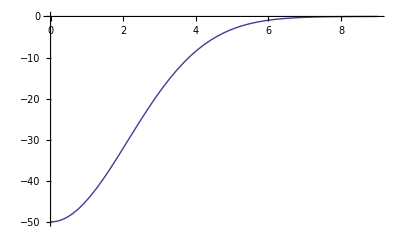

```mathematica
Plot[V[r],{r,0,3*R}]
```

```mathematica
g[L_,k_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==8},u,{r,(1000*k)^(-1),3*R},MaxSteps->20000]
```

```mathematica
u[L_,k_,r_]:=u[r]/.g[L,k][[1]]
```

```mathematica
β[L_,k_]:=3*R/Evaluate[u[L,k,3*R]]*(D[u[L,k,r],r]/.r->(3*R))-1
tanδ[L_,k_]:=N[(k*3*R*Derivative[0,1][SphericalBesselJ][L,k*3*R]-β[L,k]*SphericalBesselJ[L,k*3*R])/(k*3*R*Derivative[0,1][SphericalBesselY][L,k*3*R]-β[L,k]*SphericalBesselY[L,k*3*R])]
```

```mathematica
Table[tanδ[L,10],{L,0,3*10*R}]
```

$Aborted

ReplaceAll::reps: {1.0002837562766533` u[1.5`] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 1.5 is not a valid variable.

ReplaceAll::reps: {(1.`  + 2.4096605922012944` 2.718281828459045`^Times[« 2 »] - 0.00003064379612755102`/r^2) u[r] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {1.0002837562766533` u[1.5`] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

General::ivar: 1.5 is not a valid variable.

General::stop: Further output of General will be suppressed during this calculation.

Plot::exclul: {Re[-1.` (-1.` + Times[« 3 »]) SphericalBesselJ[L, 1.5`] + 1.5` (Times[« 2 »] + Times[« 2 »])/-1.` Plus[« 2 »] SphericalBesselY[« 2 »] + 1.5` Plus[« 2 »]] - 0} must be a list of equalities or real-valued functions.

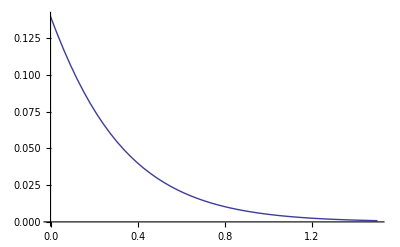

```mathematica
Plot[ArcTan[tanδ[L,1]],{L,0,3*R}]
```

```mathematica
f[k_,θ_]:=1/k*Sum[(2*L+1)*tanδ[L,k]/(1-I*tanδ[L,k])*LegendreP[L,Cos[θ]],{L,0,3*k*R}]
```

```mathematica
Abs[f[10,0]]^2
```

817.511

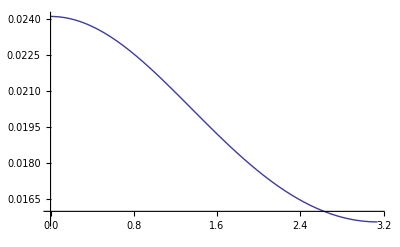

```mathematica
Plot[Abs[f[1,θ]]^2,{θ,0,Pi}]
```

```mathematica
Clear[m,ℏc,R,V,V0,Δ]
```

```mathematica
V[r_]=V0*E^(-r^2/R^2);
```

```mathematica
-m/(k*(ℏc)^2)*Assuming[Re[R^2]>0,Integrate[V[Sqrt[b^2+z^2]],{z,0,Infinity}]]
```

(3.20326 ⅇ^(-b^2/9))/k

```mathematica
Δ[k_,b_]:=-(ⅇ^(-b^2/R^2) m √π V0)/(2 k √(1/R^2) ℏc^2)
```

```mathematica
R=3 (*Femto Meter*);
V0=-50 (*Mega ElectronVolt*);
m=938.272046(*Mega ElectronVolt*);
ℏc=197.32697178(*Mega ElectronVolt^2*Femto Meter^2*);
```

```mathematica
Eif[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,k*b*θ]*(E^(2*I*Δ[k,b])-1),{b,0,Infinity}]
```

```mathematica
Table[Abs[Eif[10,θ]]^2,{θ,0,Pi,.1}]
```

{100 Abs[NIntegrate[b BesselJ[0,10 b 0.] (ⅇ^(2 ⅈ Δ[1,b])-1),{b,0,∞}]]^2,1032.08,112.064,3.63275,0.0565984,0.000523708,3.24184×10^-6,1.4479×10^-8,4.91562×10^-11,1.3164×10^-13,9.12844×10^-17,1.71804×10^-14,3.90992×10^-17,3.10958×10^-18,1.00171×10^-18,7.48569×10^-19,9.70335×10^-19,7.85631×10^-19,4.82002×10^-19,2.70262×10^-19,1.65785×10^-19,1.23379×10^-19,1.03836×10^-19,8.74932×10^-20,6.919×10^-20,5.05165×10^-20,3.4335×10^-20,2.22319×10^-20,1.41331×10^-20,8.96212×10^-21,5.45414×10^-21,2.87818×10^-21}

```mathematica
Abs[Eif[100,0]]^2
```

830.965

```mathematica
Abs[f[10,0]]^2
```

817.511